```mathematica
Neuron[i_]:={0}~Join~((2*RandomReal[]-1)&/@Range[i]);
Neuron[v_,w_]:=Join[{v},w];
Layer[n_,i_]:=Array[Neuron[i]&,n];
Network[i_,h_,o_]:={Layer[i,0],Layer[h,i],Layer[o,h]};
```

```mathematica
Compute[network_,inputs_]:=Fold[#1~Join~{Compute[#2,Last[#1]]}&,{MapThread[Join[{#1},#2]&,{inputs,Rest/@First[network]}]},Rest[network]]/;Depth[network]==4;
Compute[layer_,values_]:=Compute[#,values]&/@layer/;Depth[layer]==3;
Compute[neuron_,value_]:={LogisticSigmoid[Total[MapThread[#1*First[value[[#2]]]&,{Rest[neuron],Range[Length[neuron]-1]}]]]}~Join~Rest[neuron]/;Depth[neuron]==2;
```

```mathematica
Propagate[network_,output_,learningRate_]:=With[{outputLayer=MapThread[Propagate[#1,network[[2]],#2,learningRate]&,{Last[network],output}],hiddenLayer=network[[2]],inputLayer=First[network]},{inputLayer,MapIndexed[Propagate[#1,First[#2],inputLayer,outputLayer,output,learningRate]&,hiddenLayer],outputLayer}]/;Depth[network]==4;

Propagate[neuron_,hiddenLayer_,target_,learningRate_]:=Join[{NeuronValue[neuron]},MapThread[#1-learningRate*-NeuronValue[neuron]*(1-NeuronValue[neuron])*(target-NeuronValue[neuron])*#2&,{NeuronWeights[neuron],LayerValues[hiddenLayer]}]];

Propagate[neuron_,index_,inputLayer_,outputLayer_,target_,learningRate_]:=Join[{NeuronValue[neuron]},MapIndexed[#1-learningRate*NeuronValue[neuron]*(1-NeuronValue[neuron])*NeuronValue[inputLayer[[First[#2]]]]*Total[MapThread[(#3-#1)*-1*#1*(1-#1)*#2&,{LayerValues[outputLayer],LayerWeights[outputLayer,index],target}]]&,NeuronWeights[neuron]]]
```

## 逻辑回归

```mathematica
rate={{0.8114534494306765,0.861965039180229,0.8106575963718821},{0.8085912823752369,0.8455481526347668,0.799084144247281},{0.7707064555420219,0.8298001211387038,0.743756786102063},{0.7616580310880829,0.8637733574442436,0.7375193000514668},{0.7364532019704434,0.9617809298660362,0.7263800029757477},{0.6766198865332935,0.8096962381814524,0.6360619469026548},{0.6931422315118941,0.8432910883122108,0.645320197044335}};
```

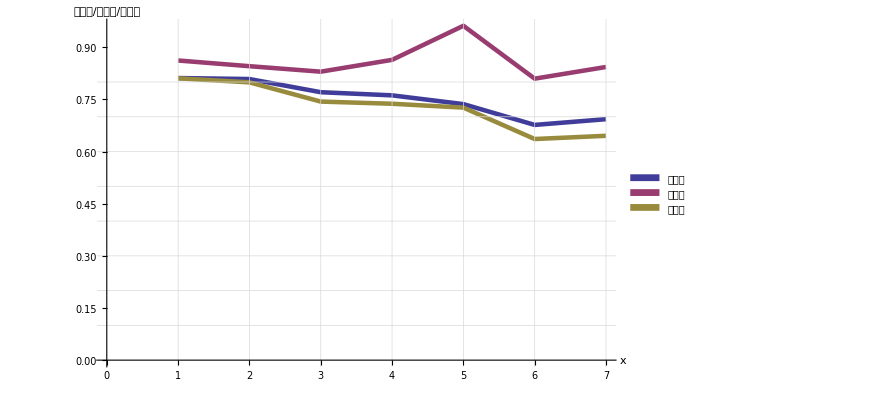

```mathematica
ListLinePlot[Transpose[rate],PlotLegends->SwatchLegend[{"精确率","召回率","准确率"},LegendFunction->Framed],AxesOrigin->{0,0},PlotStyle->Thickness[0.005],GridLines->{Range[7],Range[8]/10.0},AxesLabel->{"x","精确率/召回率/准确率"},LabelStyle->Directive[Bold,Medium]]
```

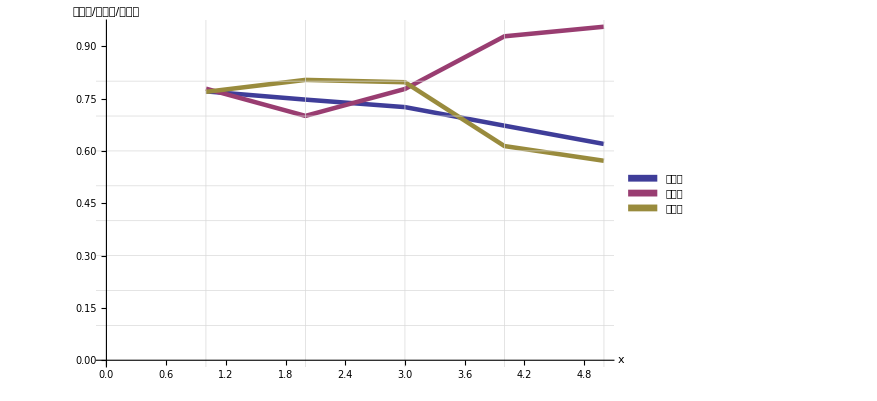

(0.770688 | 0.7784 | 0.769322
0.747072 | 0.7004 | 0.80358
0.725564 | 0.7776 | 0.796885
0.6723 | 0.928533 | 0.61392
0.619933 | 0.956 | 0.571725)

```mathematica
rateNext={{0.7706884386654571,0.7784,0.769322000395335},{0.7470720962716235,0.7004,0.8035796236805874},{0.7255644003653922,0.7776,0.7968846075015372},{0.6723,0.9285333333333333,0.6139198660025565},{0.6199333333333333,0.956,0.5717247428434734}};
ListLinePlot[Transpose[rateNext],PlotLegends->SwatchLegend[{"精确率","召回率","准确率"},LegendFunction->Framed],AxesOrigin->{0,0},PlotStyle->Thickness[0.005],GridLines->{Range[7],Range[8]/10.0},AxesLabel->{"x","精确率/召回率/准确率"},LabelStyle->Directive[Bold,Medium]]
rateNext//MatrixForm
```

### 阈值为0.4

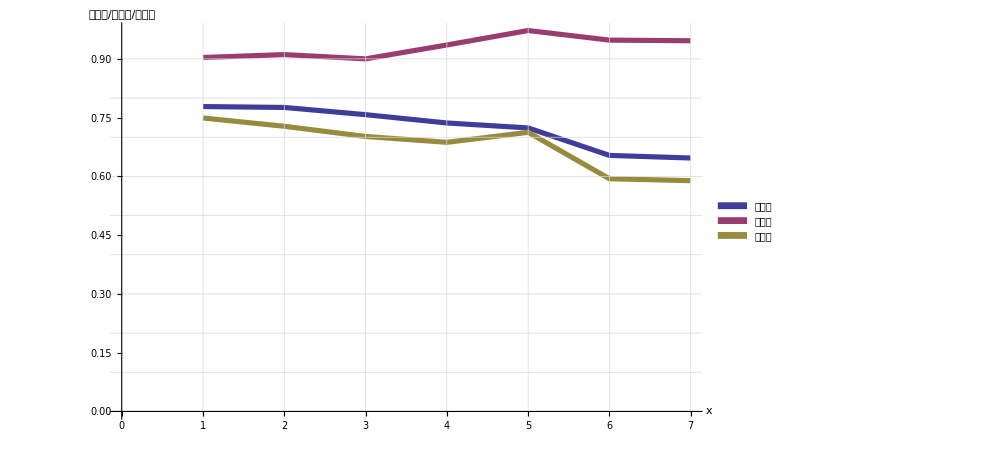

(0.778299 | 0.903556 | 0.749125
0.776058 | 0.910963 | 0.727977
0.757613 | 0.900061 | 0.701937
0.736399 | 0.935503 | 0.68703
0.723749 | 0.972419 | 0.712574
0.653628 | 0.947898 | 0.593975
0.646959 | 0.946288 | 0.589178)

```mathematica
rate4={{0.7782987273945077,0.9035563592525618,0.7491254372813593},{0.7760581174984207,0.9109630526953362,0.7279767666989352},{0.7576126674786845,0.9000605693519079,0.701936702881436},{0.7363989637305699,0.9355033152501507,0.687029659141213},{0.7237490277417682,0.9724192277383766,0.7125739858524613},{0.6536279486413855,0.9478978072822369,0.5939745367452414},{0.6469592913307455,0.9462884731442366,0.5891783567134269}};
ListLinePlot[Transpose[rate4],PlotLegends->SwatchLegend[{"精确率","召回率","准确率"},LegendFunction->Framed],AxesOrigin->{0,0},PlotStyle->Thickness[0.005],GridLines->{Range[7],Range[9]/10.0},AxesLabel->{"x","精确率/召回率/准确率"},LabelStyle->Directive[Bold,Medium]]
rate4//MatrixForm
```

## 决策树

```mathematica
jrate={{0.8492967180174146,0.8860759493670886,0.8492201039861352},{0.8218572331017057,0.8013325257419746,0.8486209108402822},{0.7935444579780755,0.7486371895820715,0.8245496997998666},{0.7801165803108808,0.8535262206148282,0.7645788336933045},{0.7653616800622245,0.9308510638297872,0.7640685640362225},{0.7032945157758534,0.8352444176222088,0.6575863161229015},{0.7150393152184732,0.8430899215449608,0.6679948995855913}};
```

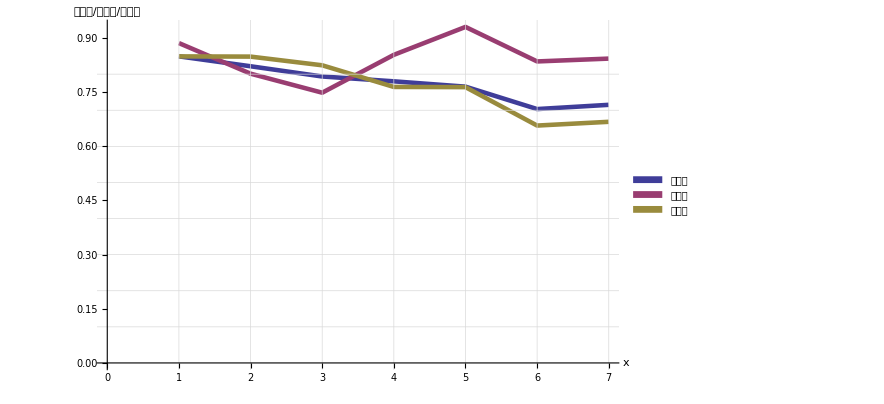

```mathematica
ListLinePlot[Transpose[jrate],PlotLegends->SwatchLegend[{"精确率","召回率","准确率"},LegendFunction->Framed],AxesOrigin->{0,0},PlotStyle->Thickness[0.005],GridLines->{Range[7],Range[8]/10.0},AxesLabel->{"x","精确率/召回率/准确率"},LabelStyle->Directive[Bold,Medium]]
```

```mathematica
(1780+2657+3703+4827)/(3389+9706+11667+8257+1780+2657+3703+4827)//N
```

0.281977

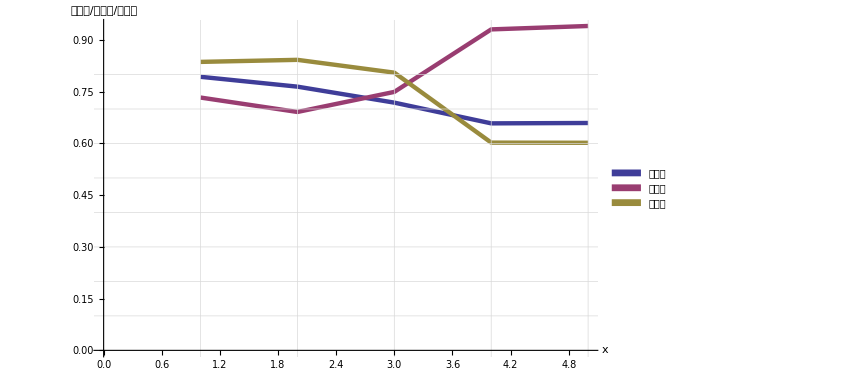

```mathematica
jrateNext={{0.7933676040721701,0.7332,0.8366042902784117},{0.7648006876544536,0.6914,0.8425542286132098},{0.7184305537430945,0.7496,0.805386433636559},{0.6583333333333333,0.9308666666666666,0.6024767000345185},{0.6594,0.9407333333333333,0.6020051194539249}};
ListLinePlot[Transpose[jrateNext],PlotLegends->SwatchLegend[{"精确率","召回率","准确率"},LegendFunction->Framed],AxesOrigin->{0,0},PlotStyle->Thickness[0.005],GridLines->{Range[7],Range[8]/10.0},AxesLabel->{"x","精确率/召回率/准确率"},LabelStyle->Directive[Bold,Medium]]
```

## agetelphones_student_rate12

```mathematica
data=Import["D:\\agetelphones_student_rate12.xls",CharacterEncoding->"UTF-8"];
data=data[[1]];
data=Select[data,#[[2]]>0&&#[[2]]≤50&];
```

```mathematica
data[[1]]
```

{0.,31.,0.615385,1.}

```mathematica
classify=SplitBy[SortBy[data,#[[1]]&],#[[1]]&];
bubbleData=(ttl=Total[#[[All,4]]];{#[[1]],#[[2]],(#[[3]])/(10ttl)}&/@#[[All,2;;4]])&/@classify;
BubbleChart[bubbleData[[1]]]
BubbleChart[bubbleData[[2]]]
```

```mathematica
BubbleChart[bubbleData]
```

```mathematica
ListPointPlot3D[bubbleData,PlotStyle->{Pink,Green},Filling->{1->{{2},Yellow}}]
```

## 添加联系人年龄区间统计和是否同城市

{{0.941088,0.997743,0.942735},{0.944713,0.993312,0.950625},{0.966767,0.998128,0.968513},{0.971601,0.998446,0.973038},{0.912113,0.99759,0.913615},{0.734159,0.954686,0.7403},{0.668431,0.751028,0.675165}}

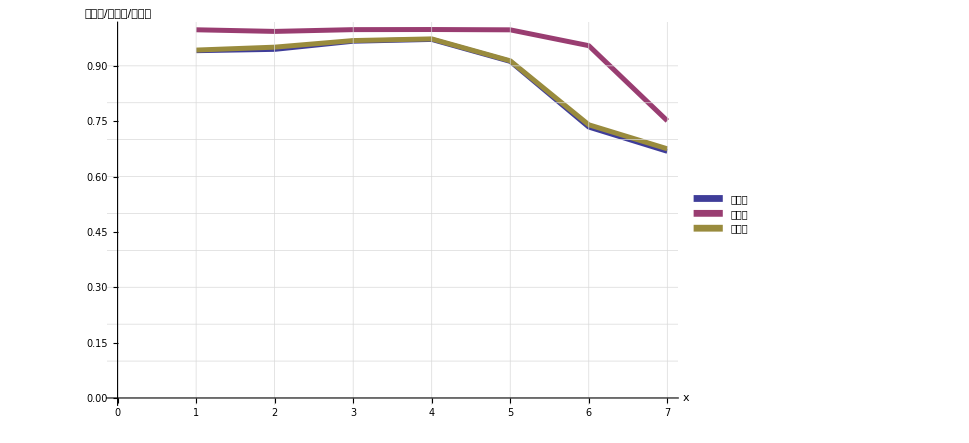

```mathematica
rate={{0.9410876132930514,0.9977433913604127,0.9427353030764545},{0.9447129909365559,0.993312101910828,0.950624809509296},{0.9667673716012085,0.9981279251170047,0.9685134726006661},{0.9716012084592145,0.9984457569163817,0.9730384731899424},{0.9121130685776849,0.997589833479404,0.9136149292665797},{0.7341589267285862,0.9546863468634686,0.7402998740986608},{0.6684309574217832,0.7510283611171249,0.6751654340210198}}
ListLinePlot[Transpose[rate],PlotLegends->SwatchLegend[{"精确率","召回率","准确率"},LegendFunction->Framed],AxesOrigin->{0,0},PlotStyle->Thickness[0.005],GridLines->{Range[7],Range[9]/10.0},AxesLabel->{"x","精确率/召回率/准确率"},LabelStyle->Directive[Bold,Medium]]
```

## 认证月份统计

### 认证月份统计.csv, 北京的时间认证方式统计.csv, 上海学生认证统计.csv

```mathematica
data=Import["D:\\上海学生认证统计.csv",CharacterEncoding->"UTF-8"];
data=data[[2;;-1]];
```

```mathematica
data[[1]]
```

{2016-02,1,24}

```mathematica
SplitBy[SortBy[data,#[[2]]&],#[[2]]&]
```

{{{2016-10,0,3},{2016-11,0,6},{2016-12,0,6},{2017-01,0,2},{2017-02,0,1},{2017-03,0,3},{2017-05,0,4},{2017-06,0,6},{2017-07,0,8},{2017-08,0,2}},{{2016-02,1,24},{2016-03,1,75},{2016-04,1,63},{2016-05,1,68},{2016-06,1,42},{2016-07,1,41},{2016-08,1,52},{2016-09,1,69},{2016-10,1,52},{2016-11,1,48},{2016-12,1,39},{2017-01,1,40},{2017-02,1,18},{2017-03,1,66},{2017-04,1,113},{2017-05,1,73},{2017-06,1,24},{2017-07,1,12},{2017-08,1,6}}}

```mathematica
alldate=Union[data[[All,1]]];
ClearAll[rate]
rate[date_,label_]:=0
(rate[#[[1]],#[[2]]]=#[[3]])&/@data;
```

```mathematica
({DateList[#],rate[#,1]/(rate[#,1]+rate[#,0])})&/@alldate
```

{{{2016,2,1,0,0,0.},1},{{2016,3,1,0,0,0.},1},{{2016,4,1,0,0,0.},1},{{2016,5,1,0,0,0.},1},{{2016,6,1,0,0,0.},1},{{2016,7,1,0,0,0.},1},{{2016,8,1,0,0,0.},1},{{2016,9,1,0,0,0.},1},{{2016,10,1,0,0,0.},52/55},{{2016,11,1,0,0,0.},8/9},{{2016,12,1,0,0,0.},13/15},{{2017,1,1,0,0,0.},20/21},{{2017,2,1,0,0,0.},18/19},{{2017,3,1,0,0,0.},22/23},{{2017,4,1,0,0,0.},1},{{2017,5,1,0,0,0.},73/77},{{2017,6,1,0,0,0.},4/5},{{2017,7,1,0,0,0.},3/5},{{2017,8,1,0,0,0.},3/4}}

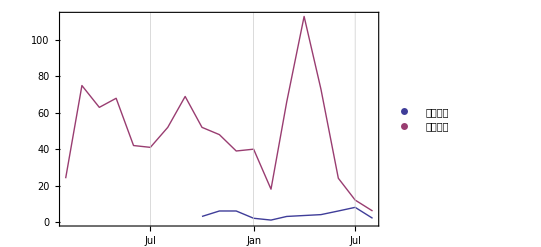

```mathematica
DateListPlot[(({DateList[#[[1]]],#[[3]]})&/@#)&/@SplitBy[SortBy[data,#[[2]]&],#[[2]]&],Joined->True,PlotLegends->{"毕业认证","学生认证"}]
```

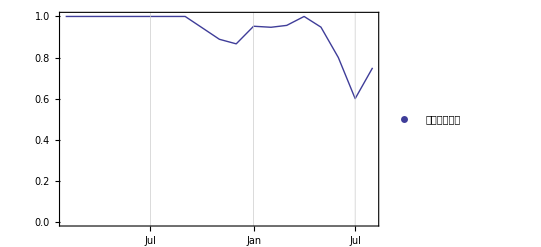

```mathematica
DateListPlot[({DateList[#],rate[#,1]/(rate[#,1]+rate[#,0])})&/@alldate,Joined->True,PlotLegends->{"学生认证比例"},PlotRange->{0,1}]
```

```mathematica
({DateList[#],rate[#,1]/(rate[#,1]+rate[#,0])})&/@alldate
```

```mathematica
DateListPlot[]
```

```mathematica
DateList["2016-02"]
```

{2016,2,1,0,0,0.}

```mathematica
a={{{0.8956011730205279,0.94065,0.9434804413239719},{0.8923370227188476,0.9367118306059007,0.9436303474355944},{0.8651383816605799,0.90705,0.9376647542254614},{0.8173759667134005,0.84165,0.9508020786262992},{0.8160028834024149,0.8345,0.9556802565277142},{0.79374392850204,0.88075,0.8576784497029896},{0.668665910196142,0.9078382838283828,0.6091794928579338},{0.668380286517239,0.8761709601873536,0.5999198236119463}},{{0.838,0.849,0.967},{0.833,0.842,0.968},{0.796,0.796,0.967},{0.675,0.659,0.973},{0.661,0.640,0.976},{0.736,0.762,0.882},{0.698,0.812,0.656},{0.698,0.767,0.650}},{{0.7029099932325739,0.68125,0.9848211058908565},{0.6926335857649738,0.6696580444600856,0.9851583398049875},{0.6592159105909271,0.62295,0.9838900734423123},{0.5011532721269956,0.4543,0.9873940447728755},{0.4859434132276086,0.43365,0.9905207857469164},{0.6200116572760832,0.57305,0.9023698921344776},{0.6932647106500243,0.6363861386138614,0.7092413793103448},{0.6850366714648023,0.5761124121779859,0.69849157054126}}};
```

```mathematica
head={"精确率","召回率", "准确率"};
pic=(ListLinePlot[a[[All,All,#]],PlotLegends->{"0.4","0.5","0.6"},AxesOrigin->{0,0},PlotLabel->head[[#]],GridLines->{Range[8],Range[10]/10},PlotRange->{{0,8},{0,1}}])&/@Range[3];
Export["D:\\逻辑回归阈值与准确率.gif",pic,"DisplayDurations"->1]
```

D:\逻辑回归阈值与准确率.gif